# Physical Neural Networks - The Harmonic Oscillator, Part I

"The career of a young theoretical physicist consists of treating the harmonic oscillator in ever-increasing levels of abstraction."  –  Sidney Coleman

I recently came across a wonderful post about constructing Physics-Informed Neural Networks by Ben Moseley. Here, the goal is to implement neural networks using Mathematica to solve a simple problem, the Harmonic Oscillator. There are also several variants to the harmonic oscillator problem, such as with damping, and other avatars of the problem appearing in RLC Circuits or, more famously, in Quantum Mechanics which would be interesting to tackle later on with neural networks.

### Notebook Setup

```mathematica
Clear[χ]
```

```mathematica
Needs["MaTeX`"];fs=18;
```

## The 1d Classical Harmonic Oscillator

The canonical problem of the harmonic oscillator is to understand a system with a restoring force F(χ)=-k*χ. For a single restoring force acting on masses connected to springs, or pendulums freely moving in a gravitational field, the system undergoes simple harmonic motion induced by the restoring force. In mathematics, the objective is to solve the system:

```mathematica
MaTeX[HoldForm[m D[χ[t],{t,2}]+k*χ[t]==0],FontSize->fs]
```

-Graphics-

The system must be supplied with some initial conditions:

```mathematica
MaTeX[{χ[0]==ξ,(D[χ[t],t]//.{t->0})==ζ},FontSize->fs]
```

{-Graphics-,-Graphics-}

Of course, there is also an exact solution. A set of representative examples starting at the equilibrium point with non-zero initial velocity is plotted below.

```mathematica
sols[t_,ξ_,ζ_,ω_]:=(DSolve[{m D[χ[t],{t,2}]+k*χ[t]==0,χ[0]==ξ,χ'[0]==ζ},{χ[t]},{t}][[1,1,2]])//.{k->ω^2*m};{MaTeX[χ[t]==FullSimplify[sols[t,ξ,ζ,ω]],FontSize->fs],MaTeX[ ω==√(k/m),FontSize->fs]}
```

{-Graphics-,-Graphics-}

```mathematica
plotsols=Table[FullSimplify[sols[t,0,1,Ω/2]],{Ω,1,5}];
```

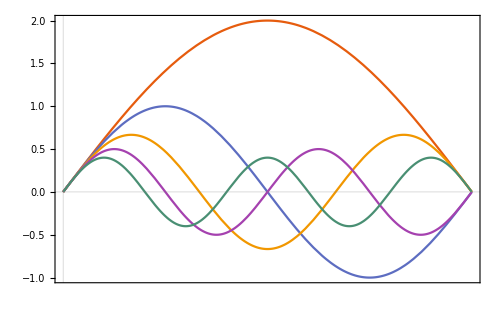

```mathematica
Plot[plotsols,{t,0,2π} ,PlotTheme->{"Scientific","MediumLines"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->10},Frame->True,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["\\chi(t)",Magnification->1.5],MaTeX["\\xi=0,\\zeta=1",Magnification->1.5]
},FrameTicks->{None,{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->1.5]},{x,2π/3*Range[0,6]}],None}},ImageSize->500,PlotLegends->{MaTeX[ω==1/2],MaTeX[ω==1],MaTeX[ω==3/2],MaTeX[ω==2],MaTeX[ω==5/2]}]
```

## Physical Neural Networks - Learning Harmonic Motion

Now, we turn to the problem of constructing neural networks with Wolfram architecture in order to learn harmonic motion directly. We will train the network for the parameters and the domain

```mathematica
MaTeX["[\\xi = 1, \\zeta = 0, \\omega={3};\\ t\\in(0,\\pi)]",FontSize->fs]
```

-Graphics-

Mathematica’s neural network algorithms can produce a trained fit to the initial sample. Here, I demonstrate how to train such Neural Networks, more documentation can be found in this post.

The algorithm is as follows. First, construct the solution with the parameters above.

```mathematica
Oscillator[t_]:=Evaluate[sols[t,1,0,3]];
```

Next, construct a data set. I chose about 30 training points for the NN.

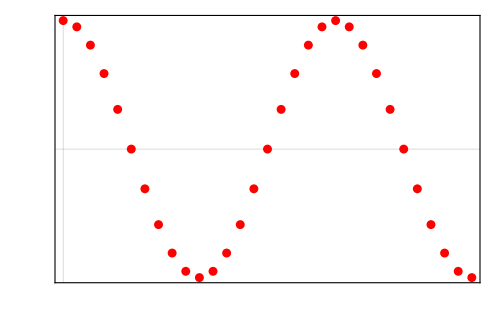

```mathematica
data=Simplify[Table[t->Oscillator[t],{t,0,π,π/30}]//N];plot=ListPlot[List@@@data,PlotTheme->{"Scientific","MediumLines"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->10},Frame->True,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["\\chi(t)",Magnification->1.5]},FrameTicks->{None,{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->1.5]},{x,π/6*Range[0,6]}],None}},ImageSize->500,PlotStyle->Red,PlotLegends->{MaTeX["{\\rm\\ \\ Training\\  Data}",FontSize->13]}]
```

Now, construct a neural network with NetChain. I chose a NN with 5 hidden layers, and 1 i-o layer respectively. The model uses different types of ElementwiseLayer, such as IntegerParts, Tanh, and LogisticSigmoid, to train the network.

```mathematica
net = NetChain[{150,Tanh,150,LogisticSigmoid,1}]
```

NetChain[<>]

Now, we can train the model with NetTrain.

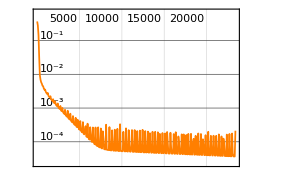
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:23404  rounds:23404  time:30s  examples/s:24248
data | ,,  training examples:31  processed examples:725524  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:3.67×10^-5
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
trainingdata=NetTrain[net,data,All,TimeGoal->30]
```

The resulting trained data can now be visualized as usual.

```mathematica
fitNN=trainingdata["TrainedNet"]
```

NetChain[<>]

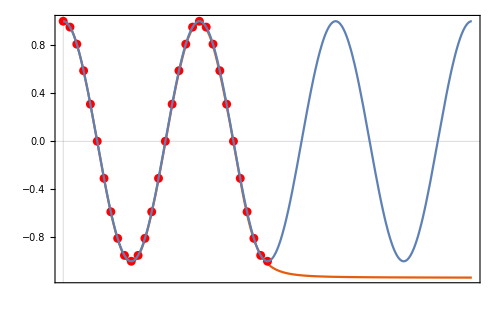

```mathematica
Show[Plot[fitNN[x],{x,0,2π},PlotTheme->{"Scientific","MediumLines"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->10},Frame->True,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["\\chi(t)",Magnification->1.5]},FrameTicks->{None,{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->1.5]},{x,π/2*Range[0,4]}],None}},ImageSize->500,PlotLegends->{MaTeX["\\rm Neural\\ Network",FontSize->13]}],plot,Plot[Oscillator[t],{t,0,2π},PlotLegends->{MaTeX["\\rm Theoretical\\ Physicist",FontSize->13]}]]
```

Lesson: The neural networks performs a good fit when trained, however fails when asked to extrapolate the result. This brings up a natural question, can we do better?

The goal of Part II is to reproduce Ben’s calculation in Physics-Informed Neural Networks by writing better neural networks which incorporates a regularization scheme where the equation of motion is simultaneously minimized along with a cost function.